```mathematica
ClearAll["`*"]
SetDirectory[NotebookDirectory[]];
Nr=30;Nx=150;Nrx=Nr*Nx;
Lx=20;
gridx=Lx/Nx Range[-Nx/2,Nx/2-1];
Gridx=gridx+Lx/4;
mu = 5.6;
```

## critical temperature

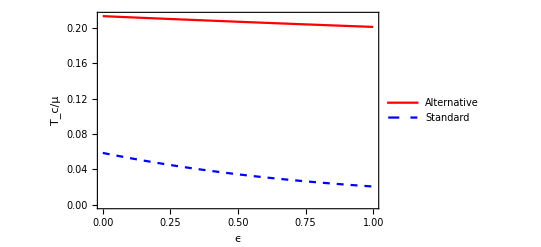

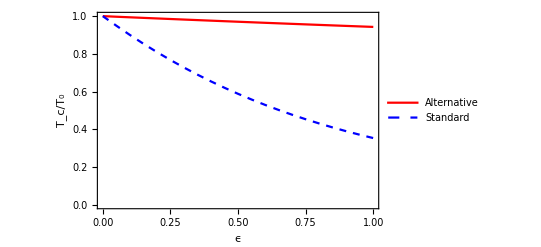

```mathematica
TcO1=Import["critical/Eigenvalue/TcO1.m"];
nTcO1=Import["critical/Eigenvalue/nTcO1.m"];
TcO2=Import["critical/Eigenvalue/TcO2.m"];
nTcO2=Import["critical/Eigenvalue/nTcO2.m"];
ListLinePlot[{TcO1,TcO2},PlotStyle->{{Red},{Blue,Dashed}},LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],PlotLegends->Placed[LineLegend[{"Alternative","Standard"},LegendFunction->Panel],{0.2,0.5}],Frame->True,FrameLabel->{Style["ϵ",14],Style["T_c/μ",14]},RotateLabel->False]
ListLinePlot[{nTcO1,nTcO2},PlotStyle->{{Red},{Blue,Dashed}},LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],PlotLegends->Placed[LineLegend[{"Alternative","Standard"},LegendFunction->Panel],{0.2,0.5}],Frame->True,FrameLabel->{Style["ϵ",14],Style["T_c/T_0",14]},RotateLabel->False]
```

## depletion

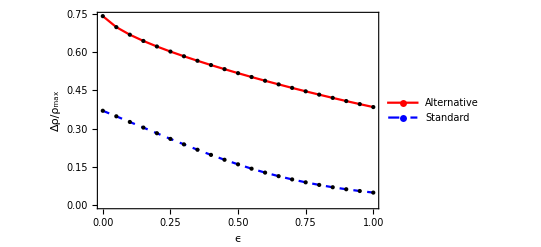

```mathematica
depletionO1=ReadList["O1/data/FixedT0.5/depletion.m"];
depletionO2=ReadList["O2/data/FixedT0.5/depletion.m"];
ListLinePlot[{depletionO1,depletionO2},PlotStyle->{{Red},{Blue,Dashed}},Epilog->{Point[depletionO1],Point[depletionO2]},PlotRange->All,LabelStyle->Directive[FontFamily->"Times New Roman", Black,12],PlotLegends->Placed[LineLegend[{"Alternative","Standard"},LegendFunction->Panel,LegendMarkers->{Style[Graphics[Point[{0,0}]],Black],Style[Graphics[Point[{0,0}]],Black]}],{0.8,0.8}],Frame->True,FrameLabel-> {Style["ϵ",14],Style["Δρ/ρ_max",14]},RotateLabel->False]
```

## Condensate

{11.3226,8.12609,7.08949,6.47213,6.03552,5.69997,5.42904,5.20143,5.00579,4.83491,4.68185,4.54453,4.41963,4.30508,4.19929,4.101,4.00921,3.92311,3.84152,3.76492,3.69234}

{1.10904,1.09257,1.0759,1.05942,1.04238,1.02457,1.00644,0.987163,0.966877,0.945439,0.922753,0.89826,0.873051,0.846805,0.819757,0.792178,0.764342,0.73649,0.709747,0.683411,0.657561}

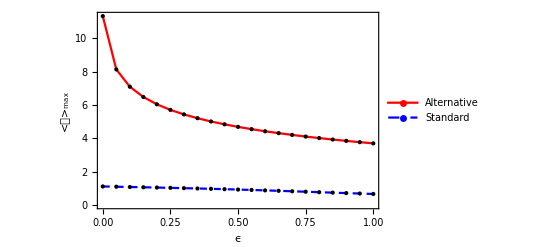

```mathematica
cdstO1=Max/@ReadList["O1/data/FixedT0.5/orderp.m"];
cdstO2=(1/mu)Max/@ReadList["O2/data/FixedT0.5/orderp.m"];
e=Range[0,1,0.05];
cdstO1
cdstO2
ListLinePlot[{Transpose[{e,cdstO1}],Transpose[{e,cdstO2}]},PlotStyle->{{Red},{Blue,Dashed}},Epilog->{Point[Transpose[{e,cdstO1}]],Point[Transpose[{e,cdstO2}]]},PlotRange->All,LabelStyle->Directive[FontFamily->"Times New Roman", Black,12],PlotLegends->Placed[LineLegend[{"Alternative","Standard"},LegendFunction->Panel,LegendMarkers->{Style[Graphics[Point[{0,0}]],Black],Style[Graphics[Point[{0,0}]],Black]}],{0.8,0.8}],Frame->True,FrameLabel-> {Style["ϵ",14],Style["<𝒪>_max",14]},RotateLabel->False]
```

## order parameter and density

```mathematica
orderpO1=Import["O1/data/orderp.m"];
densityO1=Import["O1/data/density.m"];
orderpO2=Import["O2/data/orderp.m"];
densityO2=Import["O2/data/density.m"];
```

{a→5.69547,ξ→-0.329916}

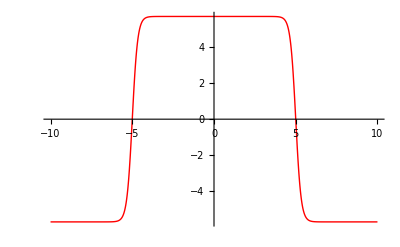

{a→26.3736,ξ→-0.322842,c→43.7384}

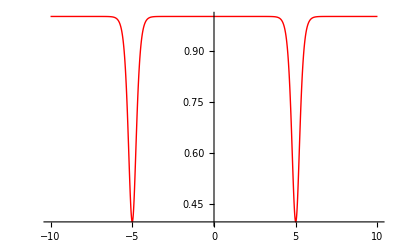

{a→5.73173,ξ→0.472301}

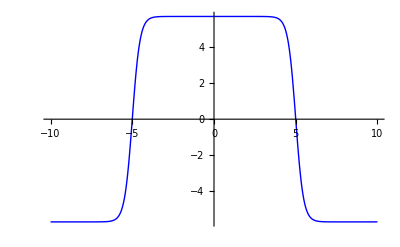

{a→2.35163,ξ→-0.539485,c→9.05454}

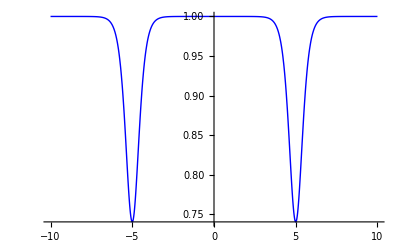

```mathematica
fitorderpO1=FindFit[Table[{gridx⟦i⟧,orderpO1⟦i⟧},{i,Nx}],a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ],{a,ξ},x]
plotorderpO1=Plot[a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ]/.fitorderpO1,{x,-Lx/2,Lx/2},PlotRange->All,PlotStyle->{Red,Thin}]
fitdensityO1=FindFit[Table[{gridx⟦i⟧,densityO1⟦i⟧},{i,Nx}],-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c,{a,ξ,c},x]
plotdensityO1=Plot[1/c(-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c)/.fitdensityO1,{x,-Lx/2,Lx/2},PlotRange->All,PlotStyle->{Red,Thin}]
fitorderpO2=FindFit[Table[{gridx⟦i⟧,orderpO2⟦i⟧},{i,Nx}],a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ],{a,ξ},x]
plotorderpO2=Plot[a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ]/.fitorderpO2,{x,-Lx/2,Lx/2},PlotRange->All,PlotStyle->{Blue,Thin}]
fitdensityO2=FindFit[Table[{gridx⟦i⟧,densityO2⟦i⟧},{i,Nx}],-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c,{a,ξ,c},x]
plotdensityO2=Plot[1/c(-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c)/.fitdensityO2,{x,-Lx/2,Lx/2},PlotRange->All,PlotStyle->{Blue,Thin}]
```

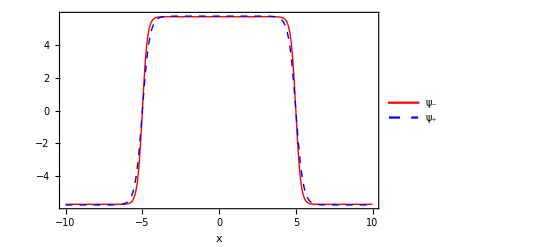

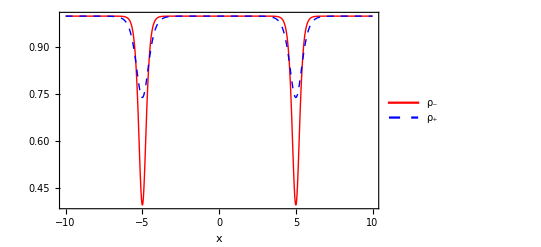

```mathematica
Plot[{a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ]/.fitorderpO1,a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ]/.fitorderpO2},{x,-Lx/2,Lx/2},PlotRange->All,PlotStyle->{{Red,Thin},{Blue,Thin,Dashed}},Axes->{False,True},Frame->True,LabelStyle->Directive[FontFamily->"Times New Roman",Black,12],PlotLegends->Placed[LineLegend[{"ψ_-","ψ_+"},LegendFunction->Panel],{0.9,0.75}],FrameLabel->Style["x",14,Italic]]
Plot[{1/c(-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c)/.fitdensityO1,1/c(-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c)/.fitdensityO2},{x,-Lx/2,Lx/2},PlotRange->All,PlotStyle->{{Red,Thin},{Blue,Thin,Dashed}},Frame->True,LabelStyle->Directive[FontFamily->"Times New Roman",Black,12],PlotLegends->Placed[LineLegend[{"ρ_-","ρ_+"},LegendFunction->Panel],{0.9,0.75}],FrameLabel->Style["x",14,Italic]]
```

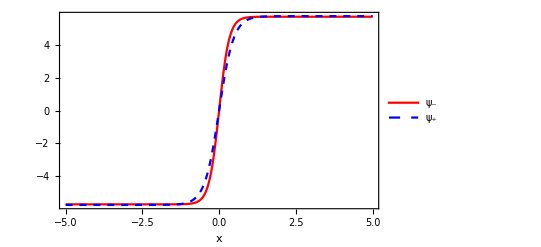

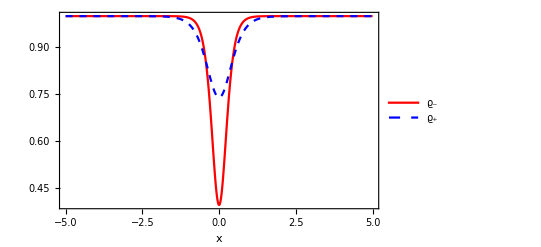

```mathematica
Plot[{(*1/mu*)a Tanh[(x-Lx/2)/ξ]Tanh[-x/ξ]/.fitorderpO1,(*1/mu^2*)a Tanh[(x-Lx/2)/ξ]Tanh[-x/ξ]/.fitorderpO2},{x,-Lx/4,Lx/4},PlotRange->All,PlotStyle->{{Red},{Blue,Dashed}},Axes->{False,True},Frame->True,LabelStyle->Directive[FontFamily->"Times New Roman",Black,12],PlotLegends->Placed[LineLegend[{"ψ_-","ψ_+"},LegendFunction->Panel],{0.9,0.2}],FrameLabel->Style["x",14,Italic]]
Plot[{1/c(-a (Sech[x/ξ]^2+Sech[(x-Lx/2)/ξ]^2)+c)/.fitdensityO1,1/c(-a (Sech[x/ξ]^2+Sech[(x-Lx/2)/ξ]^2)+c)/.fitdensityO2},{x,-Lx/4,Lx/4},PlotRange->All,PlotStyle->{{Red},{Blue,Dashed}},Frame->True,LabelStyle->Directive[FontFamily->"Times New Roman",Black,12],PlotLegends->Placed[LineLegend[{"ϱ_-","ϱ_+"},LegendFunction->Panel],{0.9,0.2}],FrameLabel->Style["x",14,Italic]]
```

## total charge change

{788.421,579.216,507.78,464.945,434.735,411.69,393.269,378.008,365.093,353.995,344.277,335.732,328.14,321.351,315.248,309.738,304.746,300.212,296.079,292.315,288.878}

{84.9257,85.1339,85.4186,85.7855,86.2212,86.7244,87.2991,87.9379,88.6429,89.4142,90.2521,91.1578,92.132,93.1742,94.2831,95.4562,96.6895,97.9786,99.3114,100.688,102.102}

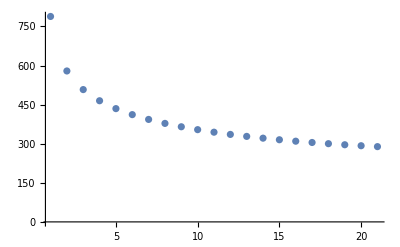

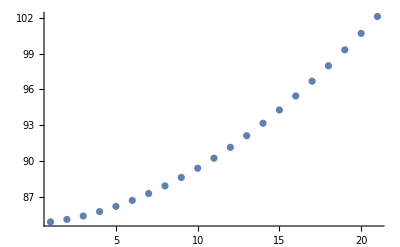

```mathematica
densityO1=ReadList["O1/data/FixedT0.5/density.m"];
densityO2=ReadList["O2/data/FixedT0.5/density.m"];
tolnumO1=1/2 Total[densityO1,{2}](Lx/Nx)
tolnumO2=1/2 Total[densityO2,{2}](Lx/Nx)
ListPlot[tolnumO1,PlotRange->All]
ListPlot[tolnumO2,PlotRange->All]
```